# Dynamic Hopf Bifurcation

```mathematica
fx[x_,y_,μ_] := -y + μ x - x(x^2 + y^2);
fy[x_,y_,μ_] := x + μ y - y(x^2 + y^2);
```

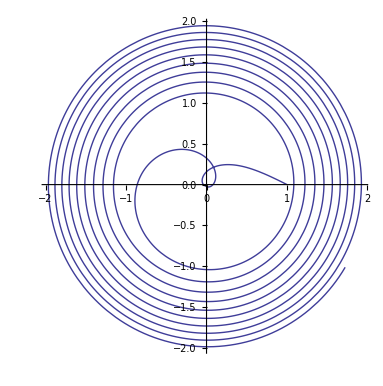

```mathematica
Clear[μ]
sol=NDSolve[{
x'[t] == fx[x[t],y[t],μ[t]],
y'[t] == fy[x[t],y[t],μ[t]],
μ'[t] ==.05,
μ[0]==-1,
x[0] ==1,
y[0]==0},{x,y,μ},{t,0,1000},MaxSteps->200000];
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,100},PlotRange->All]
```